```mathematica
Clear[CreatePlotsFinal]
```

```mathematica
CreatePlotsFinal[phase_:0,slicelength_:0.1]:=Block[{},
(*tpGp=Transpose[{10^12(#[[1]]-Mean[#[[1]]]),0.511#[[2]]}]&/@Sort[Transpose[{tp,Gp}],Mean[#1[[1]]]<Mean[#2[[1]]]&];
xpyp=Transpose[{10^3(#[[1]]),10^3#[[2]]}]&/@Sort[Transpose[{tp,xp,yp}],Mean[#1[[1]]]<Mean[#2[[1]]]&][[All,{2,3}]];*)
tpGp=SortedData[{Transpose[{avgtp[[1]],avgGp[[1]],Transpose[{10^12(#[[1]]-Mean[#[[1]]]),0.511#[[2]]}]&/@Select[Transpose[Flatten/@{tp,Gp}],Length[#[[1]]]>0&]}]}][[1]][[All,2]];
xpyp=SortedData[{Transpose[{avgtp[[1]],avgGp[[1]],Transpose[{10^3(#[[1]]),10^3#[[2]]}]&/@Select[Transpose[Flatten/@{xp,yp}],Length[#[[1]]]>0&]}]}][[1]][[All,2]];
Labeled[Framed[Column[{
ListPlot[#[[1]],Frame->True,PlotRange->{All,All},FrameLabel->{"x","y"}],
ListPlot[#[[2]],PlotRange->{All,All},Frame->True,FrameLabel->{"x","y"}],
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All}]&[{1,($CHARGE)/(slicelength Length[#[[1]]])}HistogramList[#[[1,All,1]],{slicelength}]]
(*ListLinePlot[{Map[{1,10^12}#&,SortedData[{Transpose[Map[Flatten,{avgtp,avgGp,stdtp}]]}]⟦1⟧]},Prolog->{MADDraw[$LATTICE,Offset->{0,0.025},Bends->False,WidthScale->0.05]⟦1⟧}]*)
}]
]&/@Transpose[{tpGp,xpyp}][[{Range[Length[tpGp]][[$musfocuspos]]}]],"Linac Phase = "<>ToString[NumberRight[phase]]<>"°",Top]
]
```

```mathematica
CreatePlotsFinal[text_:"",slicelength_:0.1,position_:1,opts___Rule]:=Block[{xrange},
xrange=XRange/.{opts}/.{XRange->All};
tpGp=Transpose[{10^12(t-Mean[t]),10^-6 En}];
Labeled[Framed[GraphicsColumn[{
ListPlot[#[[1]],Frame->True,PlotRange->{xrange,All},FrameLabel->{"t [ps]","p [MeV/c]"},FilterRules[{opts},Options[ListPlot]],ImageSize->Medium],
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{xrange,All},FilterRules[{opts},Options[ListPlot]],FrameLabel->{"t [ps]","I [A]"},ImageSize->Medium]&[{1,($CHARGE)/(slicelength Length[#[[1]]])}HistogramList[#[[1,All,1]],{slicelength}]],
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{xrange,All},FilterRules[{opts},Options[ListPlot]],FrameLabel->{"t [ps]","ΔE [keV]"},ImageSize->Medium]&[{HistogramList[#[[1]],{{slicelength},{10^6}}][[1,1]],10^3 StandardDeviation[#[[1,All,2]]]&/@BinLists[tpGp,slicelength,10^6]}]
}]
]&[{tpGp}],text,Top]
]
```

```mathematica
readHDF5Beam[filename_,opts___Rule]:=Block[{unrotate,verbose,cols,startposition,rotation},
unrotate=Global`HDF5Normalise/.{opts}/.{Global`HDF5Normalise->False};
verbose=Global`HDF5Verbose/.{opts}/.{Global`HDF5Verbose->False};
cols=Import[filename,"/beam/columns"];
Clear[Evaluate[#]]&/@cols;
beamdata=Transpose[Import[filename,"/beam/beam"]];
startposition=Import[filename,"/Parameters/Starting_Position"];
rotation=Import[filename,"/Parameters/Rotation"];
If[unrotate,
beamdata[[{1,2,3}]]=Transpose[(#-startposition&/@Transpose[beamdata[[{1,2,3}]]]).RotationMatrix[rotation,{0,1,0}]];
beamdata[[{4,5,6}]]=Transpose[((#&/@Transpose[beamdata[[{4,5,6}]]]).RotationMatrix[rotation,{0,1,0}])];
];
MapThread[(Evaluate[Symbol@#1]=#2)&,{cols,beamdata}];
params=Import[filename,"/Parameters"];
Clear[Evaluate[StringReplace[#1,{"_"->"£","-"->"$"}]]]&/@Keys[params];
MapThread[(Evaluate[Symbol@StringReplace[#1,{"_"->"£","-"->"$"}]]=#2)&,{Keys[params],Values[params]}];
If[verbose,
Print["Parameter(s) Assigned: ",Keys[params]];
Print["Variables(s) Assigned: ",cols];
];
]
```

```mathematica
cp:=√(cpx^2+cpy^2+cpz^2)
```

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1"]
```

\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1

```mathematica
files=FileNames["EBT-BA1-COFFIN-FOC.hdf5",{"TOMP_SC_"~~(DigitCharacter|"-")..},1];
```

```mathematica
Clear[getPhase];
getPhase[filename_String]:=StringCases[filename,"TOMP_SC_"~~phase:(DigitCharacter|"-")..~~"\\":>ToExpression[phase]][[1]]
```

```mathematica
sortedFiles=Quiet[Sort[files,getPhase[#1]<getPhase[#2]&]];
```

```mathematica
E0=QuantityMagnitude[UnitConvert[Quantity["ElectronMass"] Quantity["SpeedOfLight"]^2],"eV"]
```

510998.9

```mathematica
$CHARGE:=10^12 total£charge
```

```mathematica
En:=√(cp^2+E0^2)
```

```mathematica
readHDF5Beam[sortedFiles[[35]]]
```

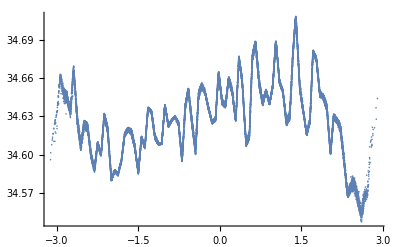

```mathematica
ListPlot[{Transpose[{10^12(t-Mean[t]),10^-6 En}]}]
```

```mathematica
StandardDeviation[t]
```

1.50508×10^-12

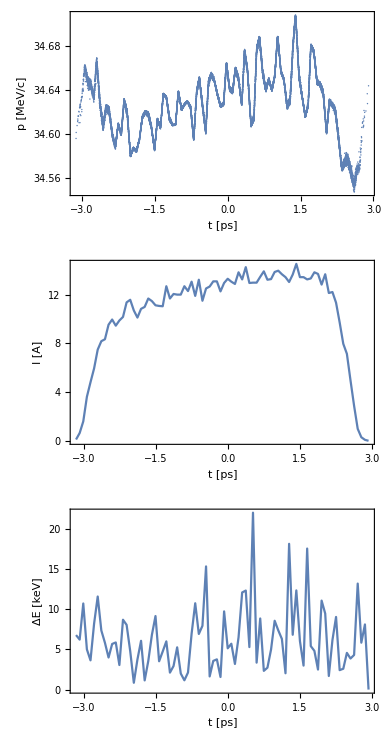
-Graphics-Phase = 15

```mathematica
CreatePlotsFinal["Phase = "~~ToString[15],0.5 10^11 StandardDeviation[t]]
```

```mathematica
sortedFiles
```

{TOMP_SC_-30\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-29\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-28\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-27\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-26\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-25\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-24\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-23\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-22\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-21\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-20\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-19\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-18\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-17\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-16\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-15\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-14\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-13\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-12\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-11\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-10\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-9\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-8\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-7\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-6\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-5\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-4\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-3\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-2\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_-1\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_0\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_1\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_2\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_3\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_4\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_5\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_6\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_7\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_8\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_9\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_10\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_11\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_12\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_13\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_14\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_15\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_16\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_17\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_18\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_19\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_20\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_21\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_22\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_23\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_24\EBT-BA1-COFFIN-FOC.hdf5,TOMP_SC_25\EBT-BA1-COFFIN-FOC.hdf5}

```mathematica
10^11 StandardDeviation[t]
```

0.0312512

```mathematica
finalPlots=Block[{},
readHDF5Beam[#];
plot=CreatePlotsFinal["Phase = "~~ToString[getPhase[#]],0.5 10^11 StandardDeviation[t]];
Export["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_BA1\\longitudinal_SC_"~~ToString[getPhase[#]]~~".png",plot,ImageResolution->200]
]&/@sortedFiles[[All]]
```

StandardDeviation::shlen: The argument {34.2951} should have at least two elements.

StandardDeviation::shlen: The argument {35.3616} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-30.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-29.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-28.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-27.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-26.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-25.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-24.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-23.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-22.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-21.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-20.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-19.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-18.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-17.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-16.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-15.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-14.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-13.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-12.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-11.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-10.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-9.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-8.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-7.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-6.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-5.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-4.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-3.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-2.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_-1.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_0.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_1.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_2.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_3.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_4.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_5.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_6.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_7.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_8.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_9.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_10.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_11.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_12.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_13.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_14.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_15.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_16.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_17.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_18.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_19.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_20.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_21.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_22.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_23.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_24.png,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_BA1\longitudinal_SC_25.png}